# HE316: Mathematica Analysis

Load packages, that’s the way life is

### SU(2) and SU(3) generators

```mathematica
<<BProbe`
```

Loaded BProbe. See the documentation for help.

### Vladimorov Package

```mathematica
<<SimpleGroupsver098b`
```

Package SimpleGroups (v.0.98β (date:06.05.10)) is loaded

Use SetGroup[] to set the group to work with.

### GroupMath Package

Will be loaded when required.

## SU(2) Representations

## 1D Representation

```mathematica
R1 = MatrixRepSU2[1]
```

{{{0}},{{0}},{{0}}}

## 2D Representation (kind of Pauli Matrices)

```mathematica
R2 = MatrixRepSU2[2]
```

{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}},{{1/2,0},{0,-1/2}}}

```mathematica
R2[[1]]
```

{{0,1/2},{1/2,0}}

```mathematica
R2[[1]]//MatrixForm
```

(0 | 1/2
1/2 | 0)

```mathematica
R2[[2]] //MatrixForm
```

(0 | -ⅈ/2
ⅈ/2 | 0)

```mathematica
R2[[3]]//MatrixForm
```

(1/2 | 0
0 | -1/2)

```mathematica
VectorOfR2 = {R2[[1]], R2[[2]], R2[[3]]};
```

```mathematica
CommutatorMatrixR2 = Table[VectorOfR2[[i]].VectorOfR2[[j]] - VectorOfR2[[j]].VectorOfR2[[i]], {i,1,3}, {j,1,3}] // Simplify // MatrixForm
```

((0 | 0
0 | 0) | (ⅈ/2 | 0
0 | -ⅈ/2) | (0 | -1/2
1/2 | 0)
(-ⅈ/2 | 0
0 | ⅈ/2) | (0 | 0
0 | 0) | (0 | ⅈ/2
ⅈ/2 | 0)
(0 | 1/2
-1/2 | 0) | (0 | -ⅈ/2
-ⅈ/2 | 0) | (0 | 0
0 | 0))

## 3D Representation [SU(2) ≅ SO(3)]

Actually, SU(2) is the double cover of SO(3). They are NOT isomorphic. This example shows how they are similar in one region.

```mathematica
T = MatrixRepSU2[3]
```

{{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}},{{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}},{{1,0,0},{0,0,0},{0,0,-1}}}

```mathematica
Tx = T[[1]]
```

{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}}

```mathematica
Ty = T[[2]]
```

{{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}}

```mathematica
Tz = T[[3]]
```

{{1,0,0},{0,0,0},{0,0,-1}}

```mathematica
VecT = {Tx, Ty, Tz};
```

```mathematica
CommutatorMatrixT = Table[VecT[[i]].VecT[[j]]-VecT[[j]].VecT[[i]], {i,1,3}, {j,1,3}] //Simplify //MatrixForm
```

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (ⅈ | 0 | 0
0 | 0 | 0
0 | 0 | -ⅈ) | (0 | -1/(√2) | 0
1/(√2) | 0 | -1/(√2)
0 | 1/(√2) | 0)
(-ⅈ | 0 | 0
0 | 0 | 0
0 | 0 | ⅈ) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | ⅈ/(√2) | 0
ⅈ/(√2) | 0 | ⅈ/(√2)
0 | ⅈ/(√2) | 0)
(0 | 1/(√2) | 0
-1/(√2) | 0 | 1/(√2)
0 | -1/(√2) | 0) | (0 | -ⅈ/(√2) | 0
-ⅈ/(√2) | 0 | -ⅈ/(√2)
0 | -ⅈ/(√2) | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

### Making a Ladder Operator Type Approach

```mathematica
Tp = (Tx + I Ty) // Simplify
```

{{0,√2,0},{0,0,√2},{0,0,0}}

```mathematica
Tm = (Tx - I Ty) // Simplify
```

{{0,0,0},{√2,0,0},{0,√2,0}}

```mathematica
{{0,0,0},{√2,0,0},{0,√2,0}}
```

{{0,0,0},{√2,0,0},{0,√2,0}}

```mathematica
RealVecT = {Tp, Tm, Tz}
```

{{{0,√2,0},{0,0,√2},{0,0,0}},{{0,0,0},{√2,0,0},{0,√2,0}},{{1,0,0},{0,0,0},{0,0,-1}}}

```mathematica
CommutatorMatrixRT = Table[RealVecT[[i]].RealVecT[[j]]-RealVecT[[j]].RealVecT[[i]], {i,1,3}, {j,1,3}] //Simplify
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{2,0,0},{0,0,0},{0,0,-2}},{{0,-√2,0},{0,0,-√2},{0,0,0}}},{{{-2,0,0},{0,0,0},{0,0,2}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{√2,0,0},{0,√2,0}}},{{{0,√2,0},{0,0,√2},{0,0,0}},{{0,0,0},{-√2,0,0},{0,-√2,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

```mathematica
StructConstRealT = {{0, 2Tz, -Tp},{-2Tz,0, Tm }, {Tp, -Tm, 0}}
```

{{0,{{2,0,0},{0,0,0},{0,0,-2}},{{0,-√2,0},{0,0,-√2},{0,0,0}}},{{{-2,0,0},{0,0,0},{0,0,2}},0,{{0,0,0},{√2,0,0},{0,√2,0}}},{{{0,√2,0},{0,0,√2},{0,0,0}},{{0,0,0},{-√2,0,0},{0,-√2,0}},0}}

```mathematica
CommutatorMatrixRT - StructConstRealT // Simplify // MatrixForm
```

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
Clear[R1, R2, Tx, Ty, Tz, Tm, Tp, T, CommutatorMatrixR2, CommutatorMatrixRT, CommutatorMatrixT, StructConstRealT, VecT, RealVecT]
```

## SU(3) Representations

## Gell-Mann Generators

```mathematica
R = MatrixRepSU3[{1,0}]
```

{{{0,1/2,0},{1/2,0,0},{0,0,0}},{{0,-ⅈ/2,0},{ⅈ/2,0,0},{0,0,0}},{{1/2,0,0},{0,-1/2,0},{0,0,0}},{{0,0,1/2},{0,0,0},{1/2,0,0}},{{0,0,-ⅈ/2},{0,0,0},{ⅈ/2,0,0}},{{0,0,0},{0,0,1/2},{0,1/2,0}},{{0,0,0},{0,0,-ⅈ/2},{0,ⅈ/2,0}},{{1/(2 √3),0,0},{0,1/(2 √3),0},{0,0,-1/(√3)}}}

```mathematica
Y = 2R[[8]]/Sqrt[3]
```

{{1/3,0,0},{0,1/3,0},{0,0,-2/3}}

```mathematica
Tz = R[[3]]
```

{{1/2,0,0},{0,-1/2,0},{0,0,0}}

```mathematica
Tp = (R[[1]]+I R[[2]])
```

{{0,1,0},{0,0,0},{0,0,0}}

```mathematica
Tm = (R[[1]]-I R[[2]])
```

{{0,0,0},{1,0,0},{0,0,0}}

```mathematica
Vp = (R[[4]]+I R[[5]])
```

{{0,0,1},{0,0,0},{0,0,0}}

```mathematica
Vm = (R[[4]]-I R[[5]])
```

{{0,0,0},{0,0,0},{1,0,0}}

```mathematica
Up1 = (R[[6]]+I R[[7]])
```

{{0,0,0},{0,0,1},{0,0,0}}

```mathematica
Um = (R[[6]]-I R[[7]])
```

{{0,0,0},{0,0,0},{0,1,0}}

```mathematica
VecR={Tp,Tm,Tz,Up1,Um,Vp,Vm,Y};
```

```mathematica
StructConstR = {{0, 2 Tz, -Tp, Vp, 0,0,-Um,0},{-2 Tz, 0, Tm,0,-Vm,Up1, 0,0},{Tp,-Tm,0,-Up1/2,Um/2,Vp/2,-Vm/2,0},{-Vp,0,Up1/2,0,3/2Y-Tz,0,Tm,-Up1},{0,Vm,-Um/2,-3/2 Y+Tz,0,-Tp,0,Um},{0,-Up1,-Vp/2,0,Tp,0,3/2 Y+Tz,-Vp},{Um,0,Vm/2,-Tm,0,-3/2 Y -Tz,0,Vm},{0,0,0,Up1,-Um,Vp,-Vm,0}};
```

```mathematica
StructConstR //MatrixForm
```

(0 | {{1,0,0},{0,-1,0},{0,0,0}} | {{0,-1,0},{0,0,0},{0,0,0}} | {{0,0,1},{0,0,0},{0,0,0}} | 0 | 0 | {{0,0,0},{0,0,0},{0,-1,0}} | 0
{{-1,0,0},{0,1,0},{0,0,0}} | 0 | {{0,0,0},{1,0,0},{0,0,0}} | 0 | {{0,0,0},{0,0,0},{-1,0,0}} | {{0,0,0},{0,0,1},{0,0,0}} | 0 | 0
{{0,1,0},{0,0,0},{0,0,0}} | {{0,0,0},{-1,0,0},{0,0,0}} | 0 | {{0,0,0},{0,0,-1/2},{0,0,0}} | {{0,0,0},{0,0,0},{0,1/2,0}} | {{0,0,1/2},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{-1/2,0,0}} | 0
{{0,0,-1},{0,0,0},{0,0,0}} | 0 | {{0,0,0},{0,0,1/2},{0,0,0}} | 0 | {{0,0,0},{0,1,0},{0,0,-1}} | 0 | {{0,0,0},{1,0,0},{0,0,0}} | {{0,0,0},{0,0,-1},{0,0,0}}
0 | {{0,0,0},{0,0,0},{1,0,0}} | {{0,0,0},{0,0,0},{0,-1/2,0}} | {{0,0,0},{0,-1,0},{0,0,1}} | 0 | {{0,-1,0},{0,0,0},{0,0,0}} | 0 | {{0,0,0},{0,0,0},{0,1,0}}
0 | {{0,0,0},{0,0,-1},{0,0,0}} | {{0,0,-1/2},{0,0,0},{0,0,0}} | 0 | {{0,1,0},{0,0,0},{0,0,0}} | 0 | {{1,0,0},{0,0,0},{0,0,-1}} | {{0,0,-1},{0,0,0},{0,0,0}}
{{0,0,0},{0,0,0},{0,1,0}} | 0 | {{0,0,0},{0,0,0},{1/2,0,0}} | {{0,0,0},{-1,0,0},{0,0,0}} | 0 | {{-1,0,0},{0,0,0},{0,0,1}} | 0 | {{0,0,0},{0,0,0},{1,0,0}}
0 | 0 | 0 | {{0,0,0},{0,0,1},{0,0,0}} | {{0,0,0},{0,0,0},{0,-1,0}} | {{0,0,1},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{-1,0,0}} | 0)

```mathematica
CommutatorMatrixR=Table[VecR[[i]].VecR[[j]]-VecR[[j]].VecR[[i]],{i,1,8},{j,1,8}] // Simplify ;
```

```mathematica
CommutatorMatrixR //MatrixForm
```

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | -1 | 0
0 | 0 | 0) | (0 | -1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | -1 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
-1 | 0 | 0) | (0 | 0 | 0
0 | 0 | 1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
-1 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | -1/2
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 1/2 | 0) | (0 | 0 | 1/2
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
-1/2 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | -1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 1/2
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | -1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
1 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | -1
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | -1/2 | 0) | (0 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | -1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 1 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | -1
0 | 0 | 0) | (0 | 0 | -1/2
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 1 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0 | 0
0 | 0 | 0
0 | 0 | -1) | (0 | 0 | -1
0 | 0 | 0
0 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1/2 | 0 | 0) | (0 | 0 | 0
-1 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
1 | 0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 1
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | -1 | 0) | (0 | 0 | 1
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
-1 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
StructConstR - CommutatorMatrixR /.{ConstantArray[0, {3,3}]->0}//Simplify //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Clear[R,Y,Tp,Tm,Tz,Vp,Vm,Up1,Um]
```

## Adjoint Representation

```mathematica
R = MatrixRepSU3[{1,1}];
```

```mathematica
Y=2R[[8]]/Sqrt[3];
```

```mathematica
Tp=(R[[1]]+I R[[2]]);
```

```mathematica
Tm=(R[[1]]- I R[[2]]);
```

```mathematica
Tz=R[[3]];
```

```mathematica
Vp=(R[[4]]+I R[[5]]);
```

```mathematica
Vm=(R[[4]]-I R[[5]]);
```

```mathematica
Upl=(R[[6]]+I R[[7]]);
```

```mathematica
Um=(R[[6]]-I R[[7]]);
```

### Killing Form

Defined as (a,b) = Tr[ad_aad_b]

if you expect it be zero, you can compute [a,[b,x]] for some x ∈ L, and then show it be zero. This kind of thing is done for the Killing forms of root vectors (later).

```mathematica
Tr[Tz.Tz]
```

3

```mathematica
Tz //MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2)

```mathematica
Eigenvectors[Tz]
```

{{0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0}}

```mathematica
Tr[Tz.Y]
```

0

```mathematica
Tr[Y.Y]
```

4

```mathematica
Tr[Tz.Tp]
```

0

```mathematica
Tr[Tz.Tm]
```

0

```mathematica
Tr[Tz.Vp]
```

0

```mathematica
Tr[Tz.Vm]
```

0

```mathematica
VecAdR = {Tz, Y, Tp, Tm, Vp, Vm, Upl, Um};
```

```mathematica
VecAdR[[1]] - Tz // Simplify
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
KillingTable = Table[Tr[VecAdR[[i]].VecAdR[[j]]], {i,1,8}, {j,1,8}] //Simplify
```

{{3,0,0,0,0,0,0,0},{0,4,0,0,0,0,0,0},{0,0,0,6,0,0,0,0},{0,0,6,0,0,0,0,0},{0,0,0,0,0,6,0,0},{0,0,0,0,6,0,0,0},{0,0,0,0,0,0,0,6},{0,0,0,0,0,0,6,0}}

```mathematica
KillingTable //MatrixForm
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 0 | 0 | 6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0)

```mathematica
X = a Tz + b Y;
```

```mathematica
X // MatrixForm
```

(a/2+b | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -a/2+b | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a/2-b | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -a/2-b)

```mathematica
Tr[X.X] //Simplify
```

3 a^2+4 b^2

Killing forms are not inner products. In particular, they are not positive definite. There is an inner product associated with the Lie Algebra but it is defined on the space containing the roots. Roots are explained below.

```mathematica
CommutatorMatrixAdR = Table[VecAdR[[i]].VecAdR[[j]]- VecAdR[[j]].VecAdR[[i]], {i,1,8}, {j,1,8}] //Simplify;
```

```mathematica
CommutatorMatrixAdR /.{Tz-> Subscript[t, z], Tp->Subscript[t, p], Tm->Subscript[t, m], Vp->Subscript[v, p], Vm->Subscript[v, m], Upl->Subscript[u, p], Um->Subscript[u, m], Y->y, ConstantArray[0,{8,8}]-> 0,-Tz-> -Subscript[t, z], -Tp->-Subscript[t, p], -Tm->-Subscript[t, m], -Vp->-Subscript[v, p], -Vm->-Subscript[v, m], -Upl->-Subscript[u, p], -Um->-Subscript[u, m], -Y->-y, 2Tz-> 2 Subscript[t, z], -2Tz->-2 Subscript[t, z], Vp/2->Subscript[v, p]/2, Vm/2->Subscript[v, m]/2, Upl/2->Subscript[u, p]/2, Um/2->Subscript[u, m]/2, -Vp/2->-Subscript[v, p]/2, -Vm/2->-Subscript[v, m]/2, -Upl/2->-Subscript[u, p]/2, -Um/2->-Subscript[u, m]/2, 3Y/2-Tz-> 3y/2-Subscript[t, z], 3Y/2+Tz-> 3y/2+Subscript[t, z],-3Y/2-Tz->- 3y/2-Subscript[t, z],-3Y/2+Tz->- 3y/2+Subscript[t, z] }//MatrixForm
```

(0 | 0 | t_p | -t_m | v_p/2 | -v_m/2 | -u_p/2 | u_m/2
0 | 0 | 0 | 0 | v_p | -v_m | u_p | -u_m
-t_p | 0 | 0 | 2 t_z | 0 | -u_m | v_p | 0
t_m | 0 | -2 t_z | 0 | u_p | 0 | 0 | -v_m
-v_p/2 | -v_p | 0 | -u_p | 0 | (3 y)/2+t_z | 0 | t_p
v_m/2 | v_m | u_m | 0 | -(3 y)/2-t_z | 0 | -t_m | 0
u_p/2 | -u_p | -v_p | 0 | 0 | t_m | 0 | (3 y)/2-t_z
-u_m/2 | u_m | 0 | v_m | -t_p | 0 | -(3 y)/2+t_z | 0)

Note that Y can form a Cartan Subalgebra only with Tz (since all the others are basis eigenvectors of ad_x if x is in the subalgebra). 

Y can form an abelian subalgebra with either of Tz, Tp, or Tm. 

To form a Cartan Subalgebra, we consider the maximally commutating subalgebra that contains a regular element (element with the smallest dimensionality of the zero eigenvalue subspace).

### Roots in the Dual Space of Cartan Subalgebra

Cartan Subalgebra is the maximally commutating Lie subalgebra. We consider that the adjoint representation means -> ad_yx = [y,x], and we are trying to represent all y ∈ g in the ad_y format. 

Dual Space is the space of linear functionals on our Lie Algebra. 
Roots lie in Dual Space of the Cartan Subalgebra (in its adjoint representation) and Root vectors are the corresponding generators. 

For α ∈ H* a root, we have a unique element (unique only for semi-simple Lie algebras) h_α∈ H, which behaves like
										α(h) = (h_α,h) 	∀ h ∈ H
Example:
X_q(aT_z + bY) = some linear combination of a and b depending on q
Here, X is the root, q is a root vector, a and b are arbitrary constants, and T_z and Y are the Cartan subalgebra elements of SU(3).

```mathematica
h1=Tz/3; h2=-1/6 Tz+Y/4; h3=Tz/6+Y/4; RootVecAdR = {h1, h2, h3};
```

```mathematica
al1=Tr[h1.(a Tz+b Y)] // Simplify
```

a

```mathematica
al2=Tr[h2.(a Tz+b Y)] // Simplify
```

-a/2+b

```mathematica
al3=Tr[h3.(a Tz+b Y)] // Simplify
```

a/2+b

h_1, h_2, h_3 belong to the Cartan subalgebra. Their Killing form with any general element of H gives the eigenvalues for roots corresponding to the root vectors t_p, u_p, v_p ∈ L-H.

```mathematica
RootKillingTable = Table[Tr[RootVecAdR[[i]].RootVecAdR[[j]]], {i,1,3}, {j,1,3}] // Simplify
```

{{1/3,-1/6,1/6},{-1/6,1/3,1/6},{1/6,1/6,1/3}}

Observe that these are positive-semidefinite.

```mathematica
RootKillingTable //MatrixForm
```

(1/3 | -1/6 | 1/6
-1/6 | 1/3 | 1/6
1/6 | 1/6 | 1/3)

Root vectors live in L-H and roots live in H* (dual space of Cartan Subalgebra). 

We can partition L as the Cartan subalgebra and the space spanned by the root vectors. 
Let Σ = {set of roots}. 
Let the set {e_α} of root vectors for α ∈ Σ be written as {e_α} = E^o. 
Then
									L = H ∪ E^o 	and		H ∩ E^o = ϕ.

We can now define <α,β> for roots α, β ∈ H* to be equal to (h_α,h_β) for the corresponding roots ∈ H*. This is a valid inner product.

### Relation between Root Vectors and SU(3) operations on 3 points (related to a later section)

```mathematica
Clear[R, Tz, Y, Upl, Um, Vm, Vp, Tm, Tp]
```

```mathematica
R=MatrixRepSU3[{1,0}];
```

```mathematica
Y=2R[[8]]/Sqrt[3];
```

```mathematica
Tp=(R[[1]]+I R[[2]]);
```

```mathematica
Tm=(R[[1]]- I R[[2]]);
```

```mathematica
Tz=R[[3]];
```

```mathematica
Vp=(R[[4]]+I R[[5]]);
```

```mathematica
Vm=(R[[4]]-I R[[5]]);
```

```mathematica
Upl=(R[[6]]+I R[[7]]);
```

```mathematica
Um = (R[[6]]-I R[[7]]);
```

```mathematica
sol = Solve[{al1 == Al1, al2 == Al2}, {a,b}]
```

{{a→Al1,b→1/2 (Al1+2 Al2)}}

```mathematica
(a Tz+ b Y).{1,0,0} /. sol// Expand
```

{{(2 Al1)/3+Al2/3,0,0}}

```mathematica
(a Tz+ b Y).{0,0,1} /. sol// Expand
```

{{0,0,-Al1/3-(2 Al2)/3}}

```mathematica
(a Tz+ b Y).{0,1,0} /. sol// Expand
```

{{0,-Al1/3+Al2/3,0}}

```mathematica
Clear[R,Y,Tp,Tm,Tz,Vp,Vm,Upl,Um];
```

```mathematica
R=MatrixRepSU3[{0,1}];
```

```mathematica
Y=2R[[8]]/Sqrt[3];
```

```mathematica
Tp=(R[[1]]+I R[[2]]);
```

```mathematica
Tm=(R[[1]]- I R[[2]]);
```

```mathematica
Tz=R[[3]];
```

```mathematica
Vp=(R[[4]]+I R[[5]]);
```

```mathematica
Vm=(R[[4]]-I R[[5]]);
```

```mathematica
Upl=(R[[6]]+I R[[7]]);
```

```mathematica
sol=Solve[{al1==Al1,al2==Al2},{a,b}]
```

{{a→Al1,b→1/2 (Al1+2 Al2)}}

```mathematica
(a Tz+ b Y).{1,0,0} /. sol// Expand
```

{{Al1/3+(2 Al2)/3,0,0}}

```mathematica
(a Tz+ b Y).{0,1,0} /. sol// Expand
```

{{0,Al1/3-Al2/3,0}}

```mathematica
(a Tz+ b Y).{0,0,1} /. sol// Expand
```

{{0,0,-(2 Al1)/3-Al2/3}}

```mathematica
Clear[R,Y,Tp,Tm,Tz,Vp,Vm,Upl,Um];
```

```mathematica
R1 = MatrixRepSU3[{1,0}];
```

```mathematica
R2= MatrixRepSU3[{0,1}];
```

```mathematica
R1-R2 //Simplify
```

{{{0,1/2,0},{1/2,0,-1/2},{0,-1/2,0}},{{0,-ⅈ/2,0},{ⅈ/2,0,ⅈ/2},{0,-ⅈ/2,0}},{{1/2,0,0},{0,-1,0},{0,0,1/2}},{{0,0,1},{0,0,0},{1,0,0}},{{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}},{{0,-1/2,0},{-1/2,0,1/2},{0,1/2,0}},{{0,ⅈ/2,0},{-ⅈ/2,0,-ⅈ/2},{0,ⅈ/2,0}},{{-1/(2 √3),0,0},{0,1/(√3),0},{0,0,-1/(2 √3)}}}

```mathematica
Clear[R1, R2];
```

## A brief discussion on definitions:

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

### Commutation Relations of Root Vectors

Let Σ be the set of all roots of the Lie Algebra L. We know by now that Σ ⊂ H* (Dual space of Cartan subalgebra of L). 
For a root α ∈ Σ (which implies α ϵ H*) and some element h ∈ H we can write (for a root vector e_α ∈ L)

										ad_h e_α = [h, e_α] = α(h)e_α 

which means that e_α is an eigenvector of the adjoint representation of any element in the Cartan subalgebra, with its eigenvalue defined by the dependency of h on the basis of H. 

By Jacobi identity, we can move forward and write immediately that:

									[h, [e_α, e_β]] = (α(h) + β(h))[e_α,e_β]

which implies one, and only one, of three things:
1.  [e_α,e_β] = 0
2. [e_α, e_β] is a root vector with root α + β
3. α + β = 0, in which case [e_α, e_β] commutes with h, and thus all elements of H. This by extension makes it an element of the Cartan subalgebra H. 

We can show that (e_α,e_β) = 0 unless α + β = 0. To show this, consider the following construction. 

for some arbitrary element x ∈ L, examine [e_α, [e_β, x]] = ad_e_αad_e_βx. From this we can possibly determine the value of (e_α, e_β).
Now, if x ∈ H, then either 1 or 2 above. In either case, there is no contribution to the trace. This is because ?
If x ∉ H, then x is a root vector. In this case, the double commutator is either zero or of the form e_(α+β+γ) and does not contribute to the trace unless α + β = 0

#### Invariance of the Killing Form

```mathematica
R = MatrixRepSU3[{1,1}];
Y=2R[[8]]/Sqrt[3];
Tp=(R[[1]]+I R[[2]]);
Tm=(R[[1]]- I R[[2]]);
Tz=R[[3]];
Vp=(R[[4]]+I R[[5]]);
Vm=(R[[4]]-I R[[5]]);
Upl=(R[[6]]+I R[[7]]);
Um=(R[[6]]-I R[[7]]);
```

```mathematica
VecR = {Y, Tp, Tm, Tz, Vp, Vm, Upl, Um};
```

```mathematica
LeftTable = Table[Tr[VecR[[i]].(VecR[[j]]VecR[[k]]-VecR[[k]]VecR[[j]])], {i,1, 8 }, {j, 1, 8}, {k, 1,8}];
```

```mathematica
RightTable= Table[Tr[(VecR[[i]]VecR[[j]]-VecR[[j]]VecR[[i]]).VecR[[k]]], {i,1, 8 }, {j, 1, 8}, {k, 1,8}];
```

```mathematica
Difference= (LeftTable - RightTable)/.{{0,0,0,0,0,0,0,0}->0}//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Killing Form is the only invariant bilinear form on a Simple Lie Algebra, up to constant scaling.
(a, [b, c]) = ([a,b], c) where a, b, c ∈ L.

```mathematica
CommutatorOfUPlusAndMinus = Upl.Um - Um.Upl
```

{{1,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-2,0},{0,0,0,0,0,0,0,-1}}

```mathematica
KillingFormOfUPlusAndMinus = Tr[Upl.Um]
```

6

```mathematica
h2 = -Tz/6 + Y/4;
```

```mathematica
Prod = KillingFormOfUPlusAndMinus*h2 //Simplify;
```

```mathematica
CommutatorOfUPlusAndMinus - Prod //Simplify //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

We have proved [e_α, e_-α] = (e_α, e_-α)h_α which means that commutator of plus and minus ladder operators is equal to their Killing form multiplied by the root vector of the plus operator.

## Representation Theory of Lie Algebras

### Definitions

The elements e_α, e_-α, and h_α have the commutation relations
1. [h_α, e_α] = α(h_α)e_α = (h_α, h_α) e_α = <α,α> e_α
2. [h_α, e_-α] = -<α,α> e_α
3. [e_α, e_-α] = (e_α, e_-α)h_α

Consider representation of elements of L as GL(V,V) for some vector space V. Let the set {H_i} denote the matrices corresponding to the elements of the Cartan subalgebra, and the set {E_α} represent the root vectors in L - H. Since all h ∈ H commute, all H_i also commute. Hence, we can choose them to be diagonal in some basis of V. 

In this basis, H_i ϕ^a=λ_i^a ϕ^a for some eigenvector ϕ^a. For some general H = Σ_i c_i H_i we can define a functional M^a(h) = Σ_i c_i λ_i^a. These are functionals on H, and thus lie in the representation of the dual space H^*.

The functionals M^a are called weights. 

In the following, Tz and Y are the Gell-Mann ({1,0}) representations of the elements of the Cartan Subalgebra of SU(3). α, β, γ are the weight vectors corresponding to each weight. 
A_igive the weights in the {1,0} rep. 
B_i give the weights in the {0,1} rep.
{1,1} is the adjoint representation.

```mathematica
Tz = DiagonalMatrix[{1/2, -1/2, 0}]
```

{{1/2,0,0},{0,-1/2,0},{0,0,0}}

```mathematica
Y = DiagonalMatrix[{1/3, 1/3, -2/3}]
```

{{1/3,0,0},{0,1/3,0},{0,0,-2/3}}

```mathematica
α = {1, 0, 0};
```

```mathematica
β= {0,1,0};
```

```mathematica
γ = {0,0,1};
```

```mathematica
H = a*Tz + b*Y
```

{{a/2+b/3,0,0},{0,-a/2+b/3,0},{0,0,-(2 b)/3}}

```mathematica
H.α
```

{a/2+b/3,0,0}

```mathematica
H.β
```

{0,-a/2+b/3,0}

```mathematica
H.γ
```

{0,0,-(2 b)/3}

```mathematica
A1={(2*Al1)/3 + Al2/3, 0, 0};
```

```mathematica
A2={0,-Al1/3+Al2/3,0};
```

```mathematica
A3={0,0,-Al1/3-(2 Al2)/3};
```

```mathematica
B1={Al1/3+(2 Al2)/3,0,0};
```

```mathematica
B2={0,Al1/3-Al2/3,0};
```

```mathematica
B3={0,0,-(2 Al1)/3-Al2/3};
```

```mathematica
Al1={1,0}/Sqrt[3]; Al2={Cos[120 Pi/180], Sin[120 Pi/180]}/Sqrt[3];
```

```mathematica
p1=A1[[1]]; p2=A2[[2]]; p3=A3[[3]];
```

```mathematica
q1=B1[[1]]; q2=B2[[2]];q3=B3[[3]];
```

Let’s generalise the creation and annihilation operators in representation theory of Lie algebras. After this subsection, you will be able to talk about: 1. {a,b} representations of SU(3), 2. Weyl Symmetry and Weyl Group, 3. Weight Space

Suppose that ϕ^a is a weight vector with weight M^a. Then, 

							Weight[E_αϕ^a] = M^a + α 	unless	E_αϕ^a = 0

This can be written more elegantly as
									HE_αϕ^a = (E_αH + α(h)E_α)ϕ^a
										    = (M^a(h) + α(h))E_αϕ^a
by noting that [H,E_α] = α(h)E_α

If M is a weight, then it lies in some series M*, M* - α, M* - 2α ... M* - qα, where M* is the highest weight and each E_-α acting on the corresponding weight vector will take it to the lower weight. 

Choosing a normalization (e_α, e_-α) = 1, we obtain [E_α, E_-α] = H_α. 

Follow equations V.11 to V.21 in Cahn to get that 
							E_α ϕ_k = r_k ϕ_(k-1)		 with 	r_k = k<M*,α>  - (k(k-1)/2)<α,α>
which gives
											q = (2<M^*,α>)/(<α,α>)
this gives us the allowed number of steps from one weight vector to another in the direction specified by α.

```mathematica
p1.Al1
```

1/6

```mathematica
p2.Al1
```

-1/6

```mathematica
p3.Al1
```

0

```mathematica
2 Transpose[p1].Al1/(Transpose[Al1].Al1)
```

1

```mathematica
2 Transpose[p2].Al1/(Transpose[Al1].Al1)
```

-1

```mathematica
2 Transpose[(p3)].Al1/(Transpose[Al1].Al1)
```

0

```mathematica
VecP = {p1, p2, p3}
```

{{1/(2 √3),1/6},{-1/(2 √3),1/6},{0,-1/3}}

```mathematica
VecQ = {q1, q2, q3}
```

{{0,1/3},{1/(2 √3),-1/6},{-1/(2 √3),-1/6}}

```mathematica
VecAl = {Al1, Al2}
```

{{1/(√3),0},{-1/(2 √3),1/2}}

```mathematica
AllowedStepsP = Table[2Transpose[VecP[[i]]].VecAl[[j]]/(Transpose[VecAl[[j]]].VecAl[[j]]), {i,1,3}, {j,1,2}] // Simplify;
```

```mathematica
AllowedStepsP //MatrixForm
```

(1 | 0
-1 | 1
0 | -1)

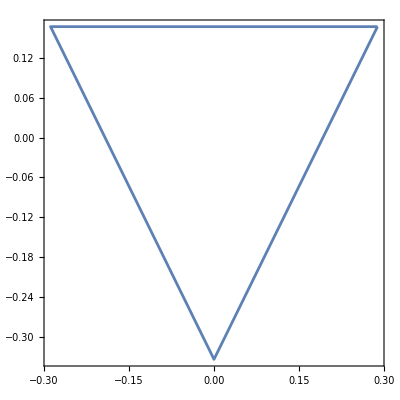

```mathematica
ListPlot[{p1,p2,p3,p1},Joined-> True,Axes-> True, Frame-> True,AspectRatio->1]
```

```mathematica
AllowedStepsQ = Table[2Transpose[VecQ[[i]]].VecAl[[j]]/(Transpose[VecAl[[j]]].VecAl[[j]]), {i,1,3}, {j,1,2}] // Simplify;
```

```mathematica
AllowedStepsQ //MatrixForm
```

(0 | 1
1 | -1
-1 | 0)

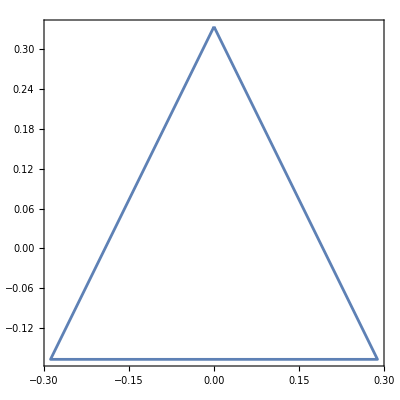

```mathematica
ListPlot[{q1,q2,q3,q1},Joined-> True,Axes-> True, Frame-> True,AspectRatio->1]
```

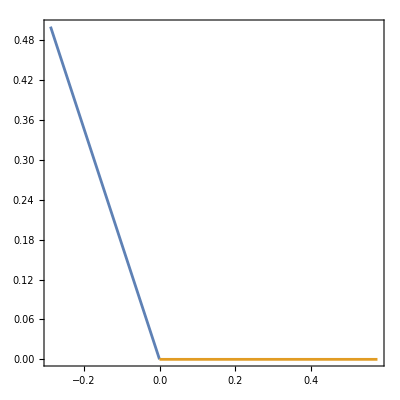

```mathematica
ListPlot[{{Al2,{0,0}},{Al1,{0,0}}},Joined-> True,Axes-> False,Frame-> True,AspectRatio->1]
```

```mathematica
SetGroup[SU[3]]
```

Set group is  A(2)

Rank of the group = 2

```mathematica
rep=BuildRep[{1,0},OutputMethod->"Weights"]  // PhysicalNormalization
```

{{{0,-1/(√3)},1},{{-1/2,1/(2 √3)},1},{{1/2,1/(2 √3)},1}}

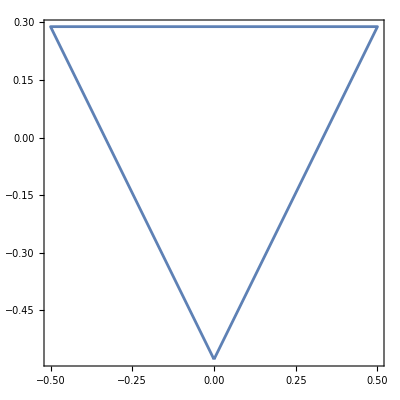

```mathematica
ListPlot[{rep[[1]][[1]],rep[[2]][[1]],rep[[3]][[1]],rep[[1]][[1]]},Joined-> True,Axes-> True, Frame-> True,AspectRatio->1]
```

```mathematica
{p1,p2,p3}*(Sqrt[3]) // Simplify
```

{{1/2,1/(2 √3)},{-1/2,1/(2 √3)},{0,-1/(√3)}}

```mathematica
antirep=BuildRep[{0,1},OutputMethod->"Weights"]  // PhysicalNormalization
```

{{{-1/2,-1/(2 √3)},1},{{1/2,-1/(2 √3)},1},{{0,1/(√3)},1}}

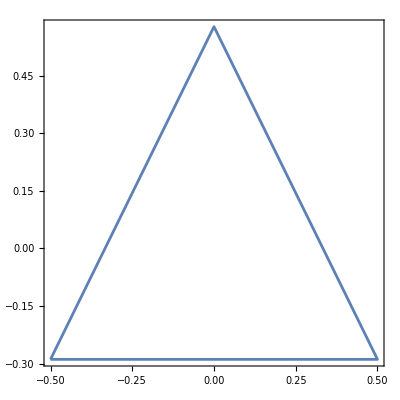

```mathematica
ListPlot[{antirep[[1]][[1]],antirep[[2]][[1]],antirep[[3]][[1]],antirep[[1]][[1]]},Joined-> True,Axes-> True, Frame-> True,AspectRatio->1]
```

```mathematica
{q1,q2,q3}*Sqrt[3] // Simplify
```

{{0,1/(√3)},{1/2,-1/(2 √3)},{-1/2,-1/(2 √3)}}

```mathematica
adj=Table[(BuildRep[{1,1},OutputMethod->"Weights"] // PhysicalNormalization)[[i]][[1]],{i,1,7}]
```

{{-1/2,-(√3)/2},{1/2,-(√3)/2},{0,0},{-1,0},{1,0},{-1/2,(√3)/2},{1/2,(√3)/2}}

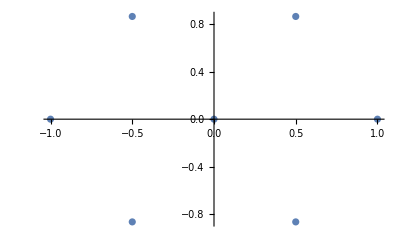

```mathematica
ListPlot[adj]
```

```mathematica
Subscript[adj, actual]=AppendTo[adj, {0,0}]
```

{{-1/2,-(√3)/2},{1/2,-(√3)/2},{0,0},{-1,0},{1,0},{-1/2,(√3)/2},{1/2,(√3)/2},{0,0}}

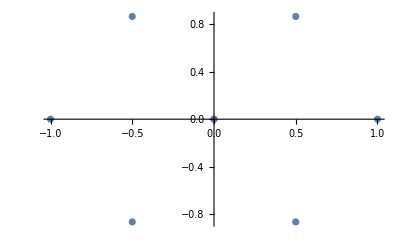

```mathematica
ListPlot[Subscript[adj, actual]](*this is shown to remind that {0,0} is present two times and the adjoint representation is eight dimensional*)
```

```mathematica
{Al1,Al2,Al1+Al2,-Al1,-Al2,-Al1-Al2} Sqrt[3] // Simplify
```

{{1,0},{-1/2,(√3)/2},{1/2,(√3)/2},{-1,0},{1/2,-(√3)/2},{-1/2,-(√3)/2}}

```mathematica
dec=Table[(BuildRep[{3,0},OutputMethod->"Weights"] // PhysicalNormalization)[[i]][[1]],{i,1,10}]
```

{{0,-√3},{-1/2,-(√3)/2},{1/2,-(√3)/2},{-1,0},{0,0},{1,0},{-3/2,(√3)/2},{-1/2,(√3)/2},{1/2,(√3)/2},{3/2,(√3)/2}}

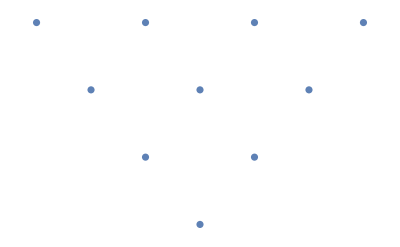

```mathematica
ListPlot[dec, Axes -> False]
```

```mathematica
Al3=Al1+Al2; Clear[VecAl]; VecAl = {Al1, Al2, Al3};
```

```mathematica
AllowedStepsDec = Table[2Transpose[dec[[i]]].VecAl[[j]]/(Transpose[VecAl[[j]]].VecAl[[j]]), {i,1,10}, {j,1,3}]/Sqrt[3] // Simplify
```

{{0,-3,-3},{-1,-1,-2},{1,-2,-1},{-2,1,-1},{0,0,0},{2,-1,1},{-3,3,0},{-1,2,1},{1,1,2},{3,0,3}}

```mathematica
AllowedStepsDec // MatrixForm
```

(0 | -3 | -3
-1 | -1 | -2
1 | -2 | -1
-2 | 1 | -1
0 | 0 | 0
2 | -1 | 1
-3 | 3 | 0
-1 | 2 | 1
1 | 1 | 2
3 | 0 | 3)

```mathematica
dec=Table[(BuildRep[{0,3},OutputMethod->"Weights"] // PhysicalNormalization)[[i]][[1]],{i,1,10}]
```

{{-3/2,-(√3)/2},{-1/2,-(√3)/2},{1/2,-(√3)/2},{3/2,-(√3)/2},{-1,0},{0,0},{1,0},{-1/2,(√3)/2},{1/2,(√3)/2},{0,√3}}

```mathematica
AllowedStepsDec = Table[2Transpose[dec[[i]]].VecAl[[j]]/(Transpose[VecAl[[j]]].VecAl[[j]]), {i,1,10}, {j,1,3}]/Sqrt[3] // Simplify;
```

```mathematica
AllowedStepsDec // MatrixForm
```

(-3 | 0 | -3
-1 | -1 | -2
1 | -2 | -1
3 | -3 | 0
-2 | 1 | -1
0 | 0 | 0
2 | -1 | 1
-1 | 2 | 1
1 | 1 | 2
0 | 3 | 3)

```mathematica
Dyn32 = BuildRep[{3,2}, OutputMethod -> "Weights"];
```

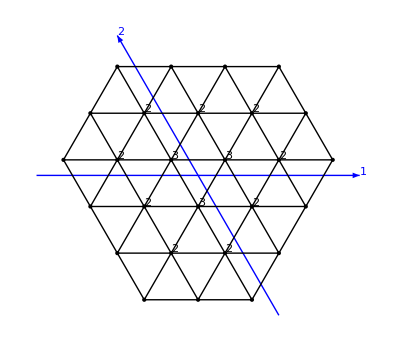

```mathematica
PlotRep2D[Dyn32, SimpleRoots]
```

```mathematica
Clear[adj]
```

```mathematica
adj = BuildRep[{1,1}, OutputMethod -> "Weights"]
```

{{{-1,0,1},1},{{0,-1,1},1},{{0,0,0},2},{{-1,1,0},1},{{1,-1,0},1},{{0,1,-1},1},{{1,0,-1},1}}

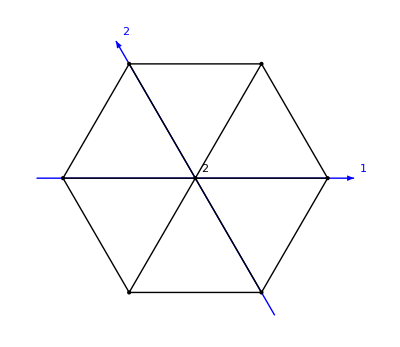

```mathematica
PlotRep2D[adj, SimpleRoots]
```

```mathematica
Dyn65 = BuildRep[{6,5}, OutputMethod -> "Weights"];
```

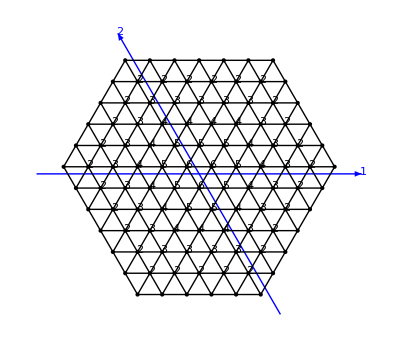

```mathematica
PlotRep2D[Dyn65, SimpleRoots]
```

### Weyl Group

Symmetries in the representations of Lie Algebras is immediately apparent in the above examples. 

Example, the minimal symmetry group in representations of SU(3) is S_2 which is deduced from {1,0} and {0,1} reps. 

A method to formally develop these group characteristics of reps of Lie Algebras is by using a symmetry which maps some weight vector to another weight vector. 
S_α : M  → M - (2<M,α>)/(<α,α>)α is an operation which maps some weight to another. This is called Weyl Reflection.

We construct the Weyl Group for irreps of Lie algebras.

Weyl Group meaning

WolframAlphaQueryResults

Some Facts, cos who wants to prove stuff when you can just demonstrate it?

1. If α ∈ Σ, then <α,α> ≠ 0
	we assumed above that our definition of inner product is a valid one, but is it though? you have to prove it using math!
2. If α ∈ Σ, then {α, -α, 0} ⊂ Σ
	not 2α or some other weird scaling of α, only α, its negative, and zero. this is true for all roots in the root space Σ
3. ∃ only one linearly independent e_α ∀ α ∈ Σ
	every weight space (except the root zero space which is the Cartan subalgebra H) is one-dimensional fr

Allowed steps in general
Assume that you are sitting at some arbitrary weight M. This weight M lies in a series M+pα ... M ... M-mα.
We know from before that m + p = (2<M+pα,α>)/(<α,α>). This is the total number of steps in this series. It can go p steps up and m steps down. 
										m - p = (2<M,α>)/(<α,α>)
gives us the difference in the number of steps to go on either side. 

Why is this important?
Consider the adjoint representation of some arbitrary Lie algebra L. 
We can show that there can exist a maximum of four weights in a string (along any given root) by the above argument. 
Assume that there are five weights WLOG labelled as β-2α, β-α, β, β+α, β+2α. Start at some root, say β+2α, and take steps in the β direction. In this direction, it is the only weight (because 2α  and 2(β +α) are not allowed). So,
						<β+2α, β> = 0 	 and 		<β-2α, β> = 0 		simultaneously
which implies that <β,β> = 0, which is impossible. Five weights in a single string are not allowed. Higher also not allowed.

Now, if the α-string of four elements. 
β + 2α is a single element in its β string
β + α is allowed to be a part of any four element β-string (which constrains m - p to ±3 or ±1)
β behaves like β + 2α
β - α behaves like β + α

Simply the results are:
1. for 4-string m - p = ±3 or ±1
2. for 3-string m - p = ±2 or 0
3. for 2-string m - p = ±1
4. for 1-string m - p = 0 

Restriction to possible angles!
Applying math twice: (<α,β><α,β>)/(<α,α><β,β>)= mn/4 = cos^2 θ_αβ
and we know the allowed values of m and n. So,the only allowed values of cos^2 θ_αβ are 0, 1/4, 1/2, 3/4.

Rational combinations of roots!
Let β = Σ_i q_iα_i. Applying math again gives us
(2<β,α_j>)/(<α_j,α_j>) = Σ_i q_i (2<α_i,α_j>)/(<α_j,α_j>) which is a linear equation in q_i with all other terms rational. Moreover, q_i come out to be integers. 

<α,β> is rational always!

### The Length and Angle between simple roots are correlated (pp. 129, Ramond)

```mathematica
{{n,npr,ArcCos[Sqrt[n npr/4]],1/Sqrt[n/npr]}/. {n->1,npr->1},{n,npr,ArcCos[-Sqrt[n npr/4]],1/Sqrt[n/npr]}/. {n->-1,npr->-1},{n,npr,ArcCos[Sqrt[n npr/4]],1/Sqrt[n/npr]}/. {n->1,npr->2},{n,npr,ArcCos[-Sqrt[n npr/4]],1/Sqrt[n/npr]}/. {n->-1,npr->-2},{n,npr,ArcCos[Sqrt[n npr/4]],1/Sqrt[n/npr]}/. {n->1,npr->3},{n,npr,ArcCos[-Sqrt[n npr/4]],1/Sqrt[n/npr]}/. {n->-1,npr->-3}}//MatrixForm
```

(1 | 1 | π/3 | 1
-1 | -1 | (2 π)/3 | 1
1 | 2 | π/4 | √2
-1 | -2 | (3 π)/4 | √2
1 | 3 | π/6 | √3
-1 | -3 | (5 π)/6 | √3)

## SU(3)

```mathematica
SetGroup[SU[3]]
```

Set group is  A(2)

Rank of the group = 2

```mathematica
SimpleRoots //PhysicalNormalization
```

{{1,0},{-1/2,(√3)/2}}

```mathematica
PosRoots = PositiveRoots //PhysicalNormalization
```

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2}}

```mathematica
CartanMatrix[SimpleRoots] //MatrixForm
```

(2 | -1
-1 | 2)

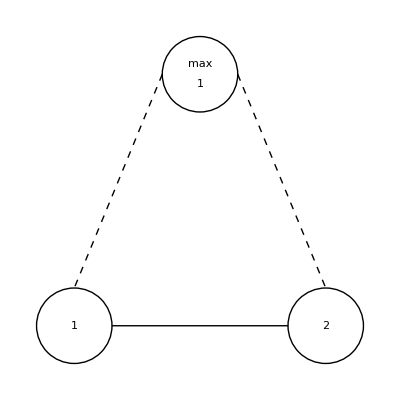

```mathematica
DynkinDiagram
```

```mathematica
rep = BuildRep[{1,0}, OutputMethod->"Weights"]
```

{{{-1/3,-1/3,2/3},1},{{-1/3,2/3,-1/3},1},{{2/3,-1/3,-1/3},1}}

```mathematica
antirep = BuildRep[{0,1}, OutputMethod -> "Weights"]
```

{{{-2/3,1/3,1/3},1},{{1/3,-2/3,1/3},1},{{1/3,1/3,-2/3},1}}

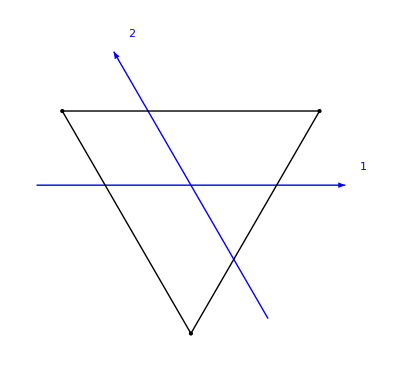

```mathematica
PlotRep2D[rep,SimpleRoots]
```

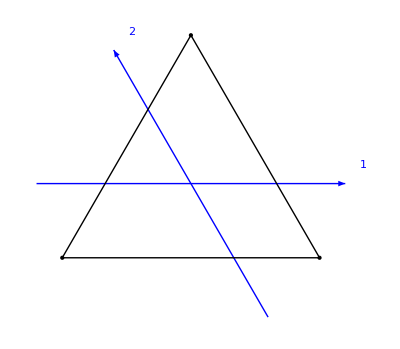

```mathematica
PlotRep2D[antirep, SimpleRoots]
```

```mathematica
rep = BuildRep[{1,0}]
```

{{{0,-1},1},{{-1,1},1},{{1,0},1}}

```mathematica
CGDecomposition[rep, rep]
```

3 ⊗ 3 = 6 ⊕ 3

{{2,0},{0,1}}

```mathematica
CGDecomposition[rep, rep, rep]
```

3 ⊗ 3 ⊗ 3 = 10 ⊕ 8 ⊕ 8 ⊕ 1

{{3,0},{1,1},{1,1},{0,0}}

```mathematica
antirep = BuildRep[{0,1}]
```

{{{-1,0},1},{{1,-1},1},{{0,1},1}}

```mathematica
CGDecomposition[rep, antirep]
```

3 ⊗ 3 = 8 ⊕ 1

{{1,1},{0,0}}

```mathematica
CGDecomposition[antirep, rep]
```

3 ⊗ 3 = 8 ⊕ 1

{{1,1},{0,0}}

```mathematica
rep2 = BuildRep[{1,1}, OutputMethod-> "Weights"]
```

{{{-1,0,1},1},{{0,-1,1},1},{{0,0,0},2},{{-1,1,0},1},{{1,-1,0},1},{{0,1,-1},1},{{1,0,-1},1}}

```mathematica
PlotRep2D[rep2, SimpleRoots]
```

-Graphics-

```mathematica
rep3 = BuildRep[{2, 0}, OutputMethod-> "Weights"]
```

{{{-2/3,-2/3,4/3},1},{{-2/3,1/3,1/3},1},{{1/3,-2/3,1/3},1},{{-2/3,4/3,-2/3},1},{{1/3,1/3,-2/3},1},{{4/3,-2/3,-2/3},1}}

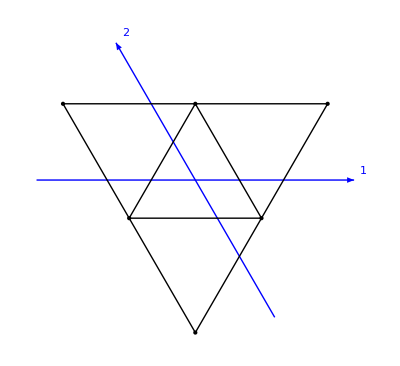

```mathematica
PlotRep2D[rep3, SimpleRoots]
```

```mathematica
rep4 = BuildRep[{3,1}, OutputMethod-> "Weights"];
```

{{{-5/3,-2/3,7/3},1},{{-2/3,-5/3,7/3},1},{{-2/3,-2/3,4/3},2},{{-5/3,1/3,4/3},1},{{1/3,-5/3,4/3},1},{{-2/3,1/3,1/3},2},{{1/3,-2/3,1/3},2},{{-5/3,4/3,1/3},1},{{4/3,-5/3,1/3},1},{{-2/3,4/3,-2/3},2},{{1/3,1/3,-2/3},2},{{4/3,-2/3,-2/3},2},{{-5/3,7/3,-2/3},1},{{7/3,-5/3,-2/3},1},{{-2/3,7/3,-5/3},1},{{1/3,4/3,-5/3},1},{{4/3,1/3,-5/3},1},{{7/3,-2/3,-5/3},1}}

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(2+√(2/3) (√(2/3)+1/(√6)))/(1/2+(√(2/3)+1/(√6))^2)+(-(1/(3 √2)-(2 √2)/3)/(√2)+((7 √(2/3))/3+1/(3 √6)) (√(2/3)+1/(√6)))/(1/2+(√(2/3)+1/(√6))^2).

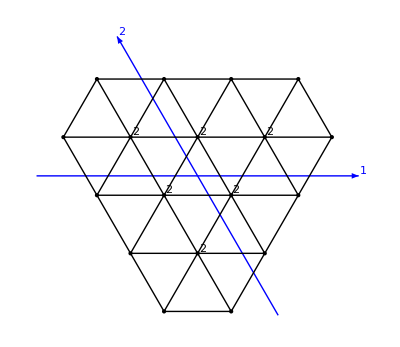

```mathematica
PlotRep2D[rep4, SimpleRoots]
```

```mathematica
Clear[rep,antirep, rep2, rep3, rep4]
```

```mathematica
rep = BuildRep[{1,0}]
```

{{{0,-1},1},{{-1,1},1},{{1,0},1}}

```mathematica
rep2 = BuildRep[{1,1}]
```

{{{-1,-1},1},{{1,-2},1},{{0,0},2},{{-2,1},1},{{2,-1},1},{{-1,2},1},{{1,1},1}}

```mathematica
rep3 = BuildRep[{2,0}]
```

{{{0,-2},1},{{-1,0},1},{{1,-1},1},{{-2,2},1},{{0,1},1},{{2,0},1}}

```mathematica
rep4 = BuildRep[{3,1}]
```

{{{-1,-3},1},{{1,-4},1},{{0,-2},2},{{-2,-1},1},{{2,-3},1},{{-1,0},2},{{1,-1},2},{{-3,1},1},{{3,-2},1},{{-2,2},2},{{0,1},2},{{2,0},2},{{-4,3},1},{{4,-1},1},{{-3,4},1},{{-1,3},1},{{1,2},1},{{3,1},1}}

```mathematica
CGDecomposition[rep, rep2, rep3]
```

3 ⊗ 8 ⊗ 6 = 35 ⊕ 27 ⊕ 27 ⊕ 10 ⊕ 10 ⊕ 10 ⊕ 8 ⊕ 8 ⊕ 8 ⊕ 1

{{4,1},{2,2},{2,2},{3,0},{3,0},{0,3},{1,1},{1,1},{1,1},{0,0}}

```mathematica
CGDecomposition[rep2, rep]
```

8 ⊗ 3 = 15 ⊕ 6 ⊕ 3

{{2,1},{0,2},{1,0}}

```mathematica
CGDecomposition[rep, rep2]
```

3 ⊗ 8 = 15 ⊕ 6 ⊕ 3

{{2,1},{0,2},{1,0}}

```mathematica
CGDecomposition[rep4, rep3, rep2]
```

24 ⊗ 6 ⊗ 8 = 105 ⊕ 36 ⊕ 90 ⊕ 90 ⊕ 48 ⊕ 48 ⊕ 48 ⊕ 48 ⊕ 60 ⊕ 60 ⊕ 21 ⊕ 42 ⊕ 42 ⊕ 42 ⊕ 42 ⊕ 42 ⊕ 42 ⊕ 15 ⊕ 15 ⊕ 15 ⊕ 15 ⊕ 24 ⊕ 24 ⊕ 24 ⊕ 24 ⊕ 15 ⊕ 15 ⊕ 15 ⊕ 15 ⊕ 15 ⊕ 6 ⊕ 6 ⊕ 3

{{6,2},{7,0},{4,3},{4,3},{5,1},{5,1},{5,1},{5,1},{2,4},{2,4},{0,5},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{4,0},{4,0},{4,0},{4,0},{1,3},{1,3},{1,3},{1,3},{2,1},{2,1},{2,1},{2,1},{2,1},{0,2},{0,2},{1,0}}

```mathematica
CGCoefficients[{0,-1}, {1,0}]
```

Part::partw: Part 1 of {} does not exist.

BuildRep::nonIntDynkin: Dynkin labels {0,-1} are not non-negative integers.

$Aborted

```mathematica
Clear[rep, antirep,rep2,rep3,rep4]
```

## SU(4)

```mathematica
SetGroup[SU[4]]
```

Set group is  A(3)

Rank of the group = 3

```mathematica
CoxeterNumber
```

4

```mathematica
CoxeterPlane
```

{{0.5,-0.5,0.5,-0.5},{0.,0.707107,-0.707107,0.}}

```mathematica
SimpleRoots
```

{{1,-1,0,0},{0,1,-1,0},{0,0,1,-1}}

```mathematica
SimpleRoots //PhysicalNormalization
```

{{1,0,0},{-1/2,(√3)/2,0},{0,-1/(√3),√(2/3)}}

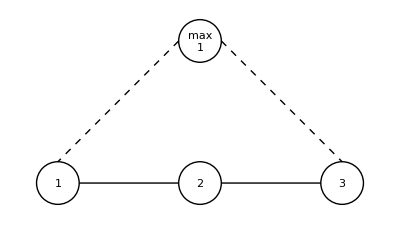

```mathematica
DynkinDiagram
```

```mathematica
CartanMatrix[SimpleRoots]
```

{{2,-1,0},{-1,2,-1},{0,-1,2}}

```mathematica
CartanMatrix[SimpleRoots] //MatrixForm
```

(2 | -1 | 0
-1 | 2 | -1
0 | -1 | 2)

```mathematica
PositiveRoots
```

{{1,-1,0,0},{1,0,-1,0},{0,1,-1,0},{1,0,0,-1},{0,1,0,-1},{0,0,1,-1}}

```mathematica
PositiveRoots //PhysicalNormalization
```

{{1,0,0},{1/2,(√3)/2,0},{-1/2,(√3)/2,0},{1/2,1/(2 √3),√(2/3)},{-1/2,1/(2 √3),√(2/3)},{0,-1/(√3),√(2/3)}}

```mathematica
CartanMatrix[PositiveRoots]
```

{{2,1,-1,1,-1,0},{1,2,1,1,0,-1},{-1,1,2,0,1,-1},{1,1,0,2,1,1},{-1,0,1,1,2,1},{0,-1,-1,1,1,2}}

```mathematica
CartanMatrix[PositiveRoots // PhysicalNormalization]
```

{{2,1,-1,1,-1,0},{1,2,1,1,0,-1},{-1,1,2,0,1,-1},{1,1,0,2,1,1},{-1,0,1,1,2,1},{0,-1,-1,1,1,2}}

```mathematica
CartanMatrix[PositiveRoots] //MatrixForm
```

(2 | 1 | -1 | 1 | -1 | 0
1 | 2 | 1 | 1 | 0 | -1
-1 | 1 | 2 | 0 | 1 | -1
1 | 1 | 0 | 2 | 1 | 1
-1 | 0 | 1 | 1 | 2 | 1
0 | -1 | -1 | 1 | 1 | 2)

```mathematica
rep = BuildRep[{1,0,0}, OutputMethod -> "Weights"]
```

{{{-1/4,-1/4,-1/4,3/4},1},{{-1/4,-1/4,3/4,-1/4},1},{{-1/4,3/4,-1/4,-1/4},1},{{3/4,-1/4,-1/4,-1/4},1}}

```mathematica
PlotRep3D[rep, SimpleRoots]
```

-Graphics3D-

```mathematica
antirep = BuildRep[{0,0,1}, OutputMethod -> "Weights"]
```

{{{-3/4,1/4,1/4,1/4},1},{{1/4,-3/4,1/4,1/4},1},{{1/4,1/4,-3/4,1/4},1},{{1/4,1/4,1/4,-3/4},1}}

```mathematica
PlotRep3D[antirep, SimpleRoots]
```

-Graphics3D-

```mathematica
rep2 = BuildRep[{1,0,1}, OutputMethod-> "Weights"]
```

{{{-1,0,0,1},1},{{0,-1,0,1},1},{{0,0,-1,1},1},{{0,0,0,0},3},{{-1,0,1,0},1},{{0,-1,1,0},1},{{-1,1,0,0},1},{{1,-1,0,0},1},{{0,1,-1,0},1},{{1,0,-1,0},1},{{0,0,1,-1},1},{{0,1,0,-1},1},{{1,0,0,-1},1}}

```mathematica
PlotRep3D[rep2, SimpleRoots]
```

-Graphics3D-

```mathematica
rep = BuildRep[{1,0,0}]
```

{{{0,0,-1},1},{{0,-1,1},1},{{-1,1,0},1},{{1,0,0},1}}

```mathematica
antirep=BuildRep[{0,0,1}]
```

{{{-1,0,0},1},{{1,-1,0},1},{{0,1,-1},1},{{0,0,1},1}}

```mathematica
CGDecomposition[rep,rep]
```

4 ⊗ 4 = 10 ⊕ 6

{{2,0,0},{0,1,0}}

```mathematica
CGDecomposition[antirep,antirep]
```

4 ⊗ 4 = 10 ⊕ 6

{{0,0,2},{0,1,0}}

```mathematica
CGDecomposition[rep,antirep]
```

4 ⊗ 4 = 15 ⊕ 1

{{1,0,1},{0,0,0}}